### Simulation of Bernoulli process

We roll a die. If we get a 6 we win, otherwise we lose.

Here is how we can simulate rolling the die 100 times.

```mathematica
trials100=Table[RandomInteger[{1,6}],{100}]
```

{3,4,1,2,4,6,5,3,5,4,5,2,5,1,1,1,1,3,1,1,5,1,3,1,5,5,6,2,6,6,6,6,1,1,1,3,6,4,3,5,5,3,3,6,3,1,4,6,3,1,6,6,5,2,2,3,6,6,3,6,1,4,4,5,3,5,3,4,4,4,4,5,5,5,1,4,3,5,5,5,6,5,1,3,6,6,1,4,3,3,2,3,5,2,5,2,2,5,6,2}

The probability of success is then estimated by the fraction of people obtaining a prize:

```mathematica
p=Count[trials100,6]/100
```

9/50

```mathematica
N[%]
```

0.18

The theoretical probability to obtain a 6 is equal to p=1/6=0.166667. 
We expect to obtain a better estimate by rolling the die more times, e.g., 1,000 times.

```mathematica
trials1000=Table[RandomInteger[{1,6}],{1000}];
```

```mathematica
p=N[Count[trials1000,6]/1000]
```

0.156

If we now roll it 10,000 times, we obtain:

```mathematica
trials10000=Table[RandomInteger[{1,6}],{10000}];
p=N[Count[trials10000,6]/10000]
```

0.1608

Plot of the distribution:

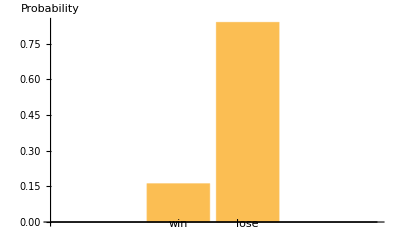

```mathematica
BarChart[{p,1-p},ChartLabels->{"win","lose"},AxesLabel->"Probability"]
```

#### The Bernoulli distribution in Wolfram Language

BernoulliDistributionpaclet:ref/BernoulliDistribution[p]  represents a Bernoulli distribution with probability parameter p.

We can use the function BernoulliDistributionpaclet:ref/BernoulliDistribution[p]  and the function PDF to calculate the probability of failure (k=0) or success (k=1) of the experiment.

```mathematica
PDF[BernoulliDistribution[1./6.],0]
```

0.833333

```mathematica
PDF[BernoulliDistribution[1./6.],1]
```

0.166667

```mathematica
N[1./6.]
```

0.166667

### Simulation of Binomial process

We now roll the die 20 times. How many times do we win?

```mathematica
trials20=RandomInteger[{1,6},20]
```

{5,3,6,3,4,3,3,2,1,1,5,1,3,1,2,4,2,2,2,1}

```mathematica
nsuccess=Count[trials20,6]
```

1

We now repeat this experiment 1,000 times. How many times do we win in each of the experiments?

```mathematica
nsuccess1000=Table[Count[RandomInteger[{1,6},20],6],{1000}];
```

```mathematica
Tally[nsuccess1000]
```

{{3,234},{1,114},{4,194},{5,145},{2,193},{6,59},{0,23},{7,23},{8,14},{9,1}}

Let’s sort the values:

```mathematica
sortTally=Sort[Tally[nsuccess1000]]
```

{{0,23},{1,114},{2,193},{3,234},{4,194},{5,145},{6,59},{7,23},{8,14},{9,1}}

If we divide by the number of experiments, we can plot the relative frequencies:

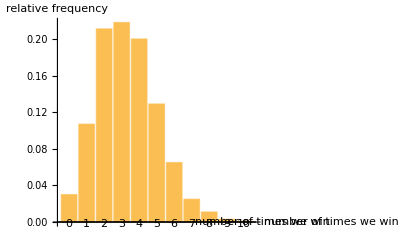

```mathematica
BarChart[sortTally[[All,2]]/1000,ChartLabels->sortTally[[All,1]],AxesLabel->{"number of times we win","relative frequency"}]
```

#### The binomial distribution in Wolfram Language

BinomialDistributionpaclet:ref/BinomialDistribution[n,p]  represents a binomial distribution with n trials and success probability p.

x \[Distributed] BinomialDistribution[n,p] (Here, \[Distributed] can be obtained by typing Esc+dist+Esc)

```mathematica
ntrials=20;
psuccess=N[1/6];
```

```mathematica
ProbSuccess=Table[{k,PDF[BinomialDistribution[ntrials,psuccess],k]},{k,0,9}]
```

{{0,0.0260841},{1,0.104336},{2,0.198239},{3,0.237887},{4,0.202204},{5,0.12941},{6,0.0647051},{7,0.0258821},{8,0.00841167},{9,0.00224311}}

Plotting together the empirical distribution simulated above and the results from BinomialDistribution function shows that both are very similar:

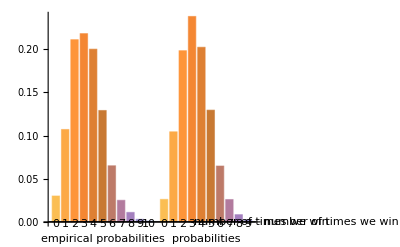

```mathematica
BarChart[{sortTally[[All,2]]/1000,ProbSuccess[[All,2]]},ChartLabels->{{"empirical probabilities","probabilities"},sortTally[[All,1]]},AxesLabel->{"number of times we win",""},ChartLayout->"Grouped"]
```

#### Expected value and variance

What is the expected result in a number of experiments? The empirical expected value is the arithmetic mean.

```mathematica
N[Mean[nsuccess1000]]
```

3.318

```mathematica
N[Variance[nsuccess1000]]
```

2.94382

The theoretical expected value are calculated as follows:

```mathematica
Expectation[x,x\[Distributed]BinomialDistribution[20,1./6.]]
```

3.33333

```mathematica
Variance[BinomialDistribution[20,1./6.]]
```

2.77778

### Distributions in Wolfram Mathematica

With the function RandomVariate we can generate random numbers drawn from a certain distribution:

```mathematica
RandomVariate[BernoulliDistribution[1./6.],10]
```

{0,0,0,1,0,0,1,0,0,0}

```mathematica
RandomVariate[BinomialDistribution[20,1./6.],10]
```

{3,4,4,1,3,3,2,4,4,5}

```mathematica
RandomVariate[PoissonDistribution[1.2],10]
```

{2,3,0,1,4,0,2,0,0,1}

```mathematica
RandomVariate[NormalDistribution[0,1],10]
```

{0.121345,-1.06376,0.356722,0.49076,1.39912,-0.310738,0.586219,-0.0619901,0.57749,-1.72797}

```mathematica
RandomVariate[ExponentialDistribution[1.2],10]
```

{2.73825,1.07127,2.11091,0.314625,0.358441,0.598833,0.313044,0.826888,0.0665002,0.0362491}

```mathematica
RandomVariate[LogNormalDistribution[0,1],10]
```

{0.256585,4.76072,0.989356,0.576914,0.609722,0.296647,0.202219,1.92226,0.226979,0.126056}

The function PDF[dist,x] gives the probability density function(probability mass function) of a certain distribution dist, evaluated at x:

```mathematica
PDF[NormalDistribution[0,1],0]
```

1/(√(2 π))

Now let’s compare the histogram of 10,000 data points obtained with RandomVariate with the theoretical PDF(PMF):

First we do that for a discrete random variable:

```mathematica
poissondata=RandomVariate[PoissonDistribution[4.8],10000];
```

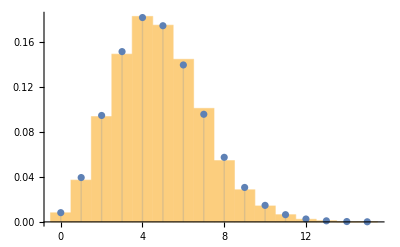

```mathematica
Show[Histogram[poissondata,100,"PDF"],DiscretePlot[PDF[PoissonDistribution[4.8],x],{x,0,15},PlotStyle->Thick,Filling->Axis,PlotRange->Full]]
```

And now for a continuous random variable:

```mathematica
normaldata=RandomVariate[NormalDistribution[0,1],10000];
```

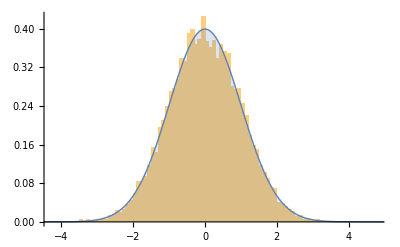

```mathematica
Show[Histogram[normaldata,100,"PDF"],Plot[PDF[NormalDistribution[0,1],x],{x,-10,10},PlotStyle->Thick,Filling->Axis,PlotRange->Full]]
```

We can also plot the empirical cumulative distribution function obtained from data, and compare it with the theoretical cumulative distribution function. For that, we first create the empirical distribution using the function EmpiricalDistribution, and then we apply the function CDF:

```mathematica
data=RandomVariate[NormalDistribution[0,1],50];
```

```mathematica
empdist=EmpiricalDistribution[data];
```

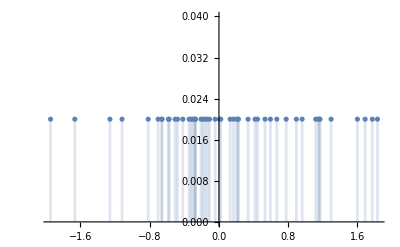
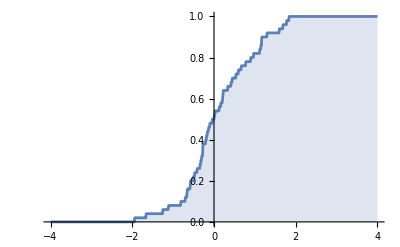

```mathematica
{DiscretePlot[PDF[empdist,x],{x,data}],DiscretePlot[CDF[empdist,x],{x,-4,4,0.01}]}
```

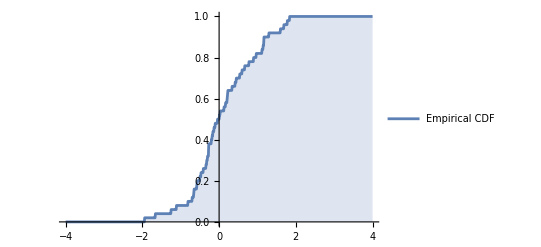

```mathematica
empCDFPlot=DiscretePlot[CDF[empdist,x],{x,-4,4,0.01},PlotLegends->{"Empirical CDF"}]
```

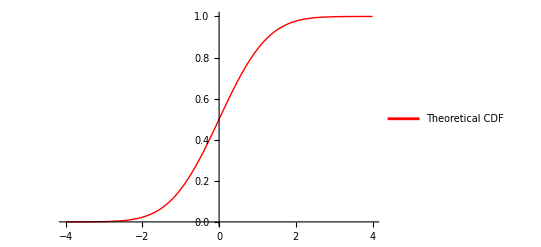

```mathematica
theoCDFPlot=Plot[CDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->{Red,Thick},PlotLegends->{"Theoretical CDF"}]
```

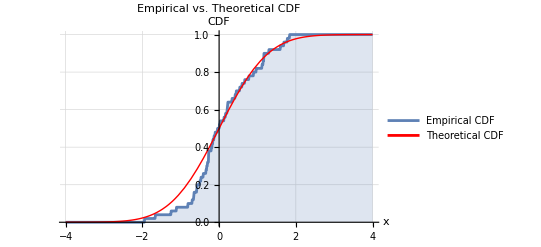

```mathematica
Show[empCDFPlot,theoCDFPlot,AxesLabel->{"x","CDF"},PlotRange->All,GridLines->Automatic,PlotLabel->"Empirical vs. Theoretical CDF"]
```